```mathematica
SetDirectory@NotebookDirectory[]
```

/Users/leima/github/neuphysics/codebase/neupackage/mma/package-test

```mathematica
Get["../dispersion-relation.wl"]
```

```mathematica
pltcolors=ColorData[97,"ColorList"]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

## Define Beams

```mathematica
NBeamsLR[4]
```

{{-π/2,0.451027},{-π/2,0.795399},{π/2,1.0472},{π/2,1.2661}}

```mathematica
spectDBWC1={{1,-0.6},{1,0.6}}
spectDBWC2={{0.5,-0.6},{1,0.6}}
spectDBWC3={{0.1,-0.6},{1,0.6}}
```

{{1,-0.6},{1,0.6}}

{{0.5,-0.6},{1,0.6}}

{{0.1,-0.6},{1,0.6}}

```mathematica
spectDBC1={{-1,-0.6},{1,0.6}}
spectDBC2={{-0.5,-0.6},{1,0.6}}
spectDBC3={{-0.1,-0.6},{1,0.6}}
```

{{-1,-0.6},{1,0.6}}

{{-0.5,-0.6},{1,0.6}}

{{-0.1,-0.6},{1,0.6}}

```mathematica
spectDBAbs={{g1,u1},{g2,u2}}
```

{{g1,u1},{g2,u2}}

```mathematica
spectDBWC4={{0.1,-0.7},{1,0.6}}
spectDBC4={{-0.1,-0.7},{1,0.6}}
```

{{0.1,-0.7},{1,0.6}}

{{-0.1,-0.7},{1,0.6}}

## Define Useful Functions

```mathematica
DBPltDR[spect_]:=Module[{spectM},

spectM=spect;

ParametricPlot[
{DBAxialSymKNMAA[spectM, n],DBAxialSymOmegaNMAA[spectM, n]},
{n,-20,20},
PlotRange->{{-2,2},{-2,2}},
Exclusions->((n #[[2]]==1)&/@spectM),ExclusionsStyle->Directive[Dashed,LightGray],
PlotTheme->"Scientific",Frame->True,ImageSize->Large,PlotLabel->"DR for spectrum "<>ToString[spectM],FrameLabel->{"k","ω"}
]
]
```

```mathematica
DBPltOmegaN[spect_,range_:{{-10,10},{-1,1}}]:=Module[{spectM},

spectM=spect;

Plot[
DBAxialSymOmegaNMAA[spectM, n],
{n,range[[1,1]],range[[1,2]]},
PlotRange->range,
Exclusions->((n #[[2]]==1)&/@spectM),ExclusionsStyle->Directive[Dashed,LightGray],
PlotTheme->"Scientific",Frame->True,ImageSize->Large,PlotLabel->"ω(n) for spectrum "<>ToString[spectM],FrameLabel->{"k","ω"}
]
]
```

```mathematica
DBPltKN[spect_,range_:{{-10,10},{-1,1}}]:=Module[{spectM},

spectM=spect;

Plot[
DBAxialSymKNMAA[spectM, n],
{n,range[[1,1]],range[[1,2]]},
PlotRange->range,
Exclusions->((n #[[2]]==1)&/@spectM),ExclusionsStyle->Directive[Dashed,LightGray],
PlotTheme->"Scientific",Frame->True,ImageSize->Large,PlotLabel->"k(n) for spectrum "<>ToString[spectM],FrameLabel->{"k","ω"}
]
]
```

## Calculate DR

Test Functions

```mathematica
DBAxialSymIntFun0nTotal[spectDBC2,n]
DBAxialSymIntFun1nTotal[spectDBC2,n]
DBAxialSymIntFun2nTotal[spectDBC2,n]
```

1/(1-0.6 n)-0.5/(1+0.6 n)

0.6/(1-0.6 n)+0.3/(1+0.6 n)

0.36/(1-0.6 n)-0.18/(1+0.6 n)

```mathematica
DBAxialSymOmegaNMAA[spectDBC1, n]
```

1/4 (0.64/(1-0.6 n)-0.64/(1+0.6 n))

```mathematica
DBAxialSymKNMAA[spectDBC1, n]
```

1/4 (0.64/(1-0.6 n)-0.64/(1+0.6 n)) n

Compare with the previous functions

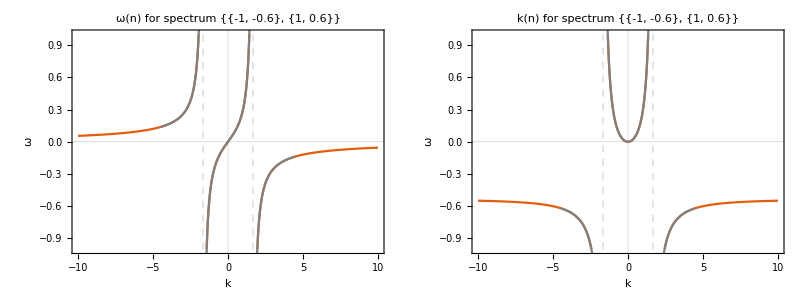

```mathematica
Grid@{{
Show[
DBPltOmegaN[spectDBC1],
NBeamsOmegaNPlt[spectDBC1]
],
Show[
DBPltKN[spectDBC1],
NBeamsKNPlt[spectDBC1]
]
}}
```

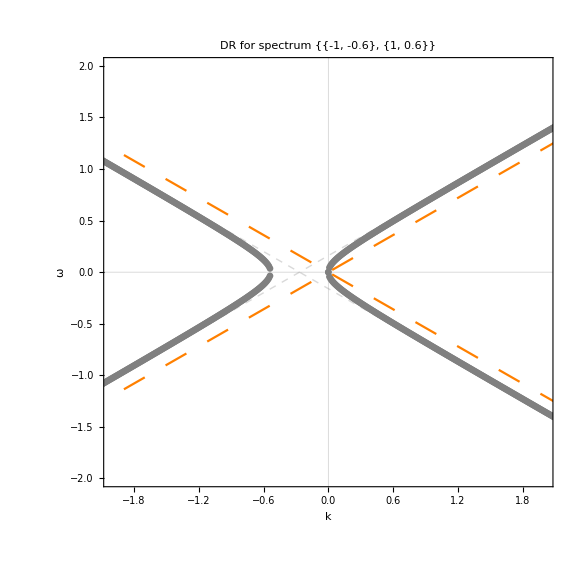

```mathematica
Show[
DBPltDR[spectDBC1],NBeamsOmegaKPlt[spectDBC1][[2]]
]
```

## About Singularities in MZA solution

Numerical Test

```mathematica
DBAxialSymIntFun0nTotal[spectDBC1,n] + DBAxialSymIntFun2nTotal[spectDBC1,n] -2 DBAxialSymIntFun1nTotal[spectDBC1,n]//FullSimplify
```

(6.66667-4.53333 n)/(-2.77778+1. n^2)

```mathematica
testMZA1[n_]:=Sqrt[ (DBAxialSymIntFun0nTotal[spectDBC1,n] + DBAxialSymIntFun2nTotal[spectDBC1,n] -2 DBAxialSymIntFun1nTotal[spectDBC1,n])(DBAxialSymIntFun0nTotal[spectDBC1,n] + DBAxialSymIntFun2nTotal[spectDBC1,n] + 2 DBAxialSymIntFun1nTotal[spectDBC1,n]) ]//FullSimplify
```

```mathematica
Limit[
testMZA1[n],
n->1/0.6
]
```

∞

```mathematica
testMZA1[n]
```

√((-44.4444+20.5511 n^2)/(7.71605-5.55556 n^2+1. n^4))

```mathematica
testMZA2[n_]:=DBAxialSymIntFun0nTotal[spectDBC1,n] - DBAxialSymIntFun2nTotal[spectDBC1,n]//FullSimplify
```

```mathematica
Limit[
testMZA2[n],
n->1/0.6
]
```

-∞

```mathematica
DBAxialSymOmegaNMZA[spectDBC1,1/0.6]
```

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power :: infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression ComplexInfinity + ComplexInfinity + ComplexInfinity encountered.

General::stop: Further output of Infinity :: indet will be suppressed during this calculation.

{Indeterminate,Indeterminate}

```mathematica
Limit[
DBAxialSymOmegaNMZA[spectDBC1,n],
n->1/0.6
]
```

{-0.5625,∞}

Analytical

```mathematica
testI0pI2mI1[n_]:=DBAxialSymIntFun0nTotal[spectDBAbs,n] + DBAxialSymIntFun2nTotal[spectDBAbs,n] -2 DBAxialSymIntFun1nTotal[spectDBAbs,n]
```

```mathematica
testI0pI2pI1[n_]:=DBAxialSymIntFun0nTotal[spectDBAbs,n] + DBAxialSymIntFun2nTotal[spectDBAbs,n] +2 DBAxialSymIntFun1nTotal[spectDBAbs,n]
```

```mathematica
testI0pI2mI1[n]//FullSimplify
testI0pI2pI1[n]//FullSimplify
```

-(g2 (-1+n u1) (-1+u2)^2+g1 (-1+u1)^2 (-1+n u2))/((-1+n u1) (-1+n u2))

-(g2 (-1+n u1) (1+u2)^2+g1 (1+u1)^2 (-1+n u2))/((-1+n u1) (-1+n u2))

```mathematica
testI0pI2mI1[n]testI0pI2pI1[n]//FullSimplify
```

((g2 (-1+n u1) (-1+u2)^2+g1 (-1+u1)^2 (-1+n u2)) (g2 (-1+n u1) (1+u2)^2+g1 (1+u1)^2 (-1+n u2)))/((-1+n u1)^2 (-1+n u2)^2)

```mathematica
Sqrt[testI0pI2mI1[n]testI0pI2pI1[n]]//FullSimplify
```

√(((g2 (-1+n u1) (-1+u2)^2+g1 (-1+u1)^2 (-1+n u2)) (g2 (-1+n u1) (1+u2)^2+g1 (1+u1)^2 (-1+n u2)))/((-1+n u1)^2 (-1+n u2)^2))

```mathematica
testI0mI2[n_]:=DBAxialSymIntFun0nTotal[spectDBAbs,n] - DBAxialSymIntFun2nTotal[spectDBAbs,n]
```

```mathematica
testI0mI2[n]//FullSimplify
```

(g1 (-1+u1^2) (-1+n u2)+g2 (-1+n u1) (-1+u2^2))/((-1+n u1) (-1+n u2))

```mathematica
Limit[
testI0mI2[n],
n->1/u1
]
```

DirectedInfinity[Sign[g1 (-1+u1^2)]/Sign[u1]]

```mathematica
Limit[
Sqrt[testI0pI2mI1[n]testI0pI2pI1[n]],
n->1/u1
]
```

DirectedInfinity[√((Sign[g1]^2 Sign[-1+u1^2]^2)/Sign[u1]^2)]

```mathematica
testI0mI2[n]+Sqrt[testI0pI2mI1[n]testI0pI2pI1[n]]//FullSimplify
```

(g1 (-1+u1^2))/(-1+n u1)+(g2 (-1+u2^2))/(-1+n u2)+√(((g2 (-1+n u1) (-1+u2)^2+g1 (-1+u1)^2 (-1+n u2)) (g2 (-1+n u1) (1+u2)^2+g1 (1+u1)^2 (-1+n u2)))/((-1+n u1)^2 (-1+n u2)^2))

```mathematica
Limit[
testI0mI2[n]+Sqrt[testI0pI2mI1[n]testI0pI2pI1[n]],
n->1/u1
]
```

DirectedInfinity[g1 (-1/u1+u1)+√((g1^2 (-1+u1^2)^2)/u1^2)]

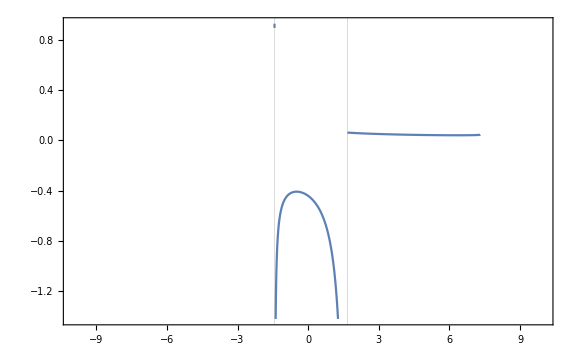

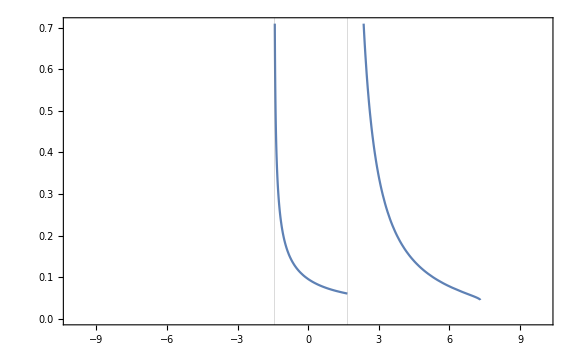

```mathematica
Plot[
Evaluate@DBAxialSymOmegaNMZA[spectDBC4,n][[1]],
{n,-10,10},Exclusions->{1/spectDBC4[[1,2]],1/spectDBC4[[2,2]]},ExclusionsStyle->Red,Frame->True,ImageSize->Large,GridLines->{{1/spectDBC4[[1,2]],1/spectDBC4[[2,2]]},None}
]

Plot[
Evaluate@DBAxialSymOmegaNMZA[spectDBC4,n][[2]],
{n,-10,10},Exclusions->{1/spectDBC4[[1,2]],1/spectDBC4[[2,2]]},ExclusionsStyle->Red,Frame->True,ImageSize->Large,GridLines->{{1/spectDBC4[[1,2]],1/spectDBC4[[2,2]]},None}
]
```

```mathematica
DBAxialSymOmegaNMZA[spectDBC4,1/spectDBC4[[2,2]]]//Quiet
Limit[
DBAxialSymOmegaNMZA[spectDBWC4,n],
n->1/spectDBC4[[1,2]]
]//Quiet

DBAxialSymOmegaNMZA[spectDBC4,1/spectDBC4[[2,2]]]//Quiet
Limit[
DBAxialSymOmegaNMZA[spectDBC4,n],
n->1/spectDBC4[[1,2]]
]//Quiet
```

{Indeterminate,Indeterminate}

{-∞,0.892157}

{Indeterminate,Indeterminate}

{0.892157,∞}